```mathematica
x0=0.;
y0=0.;
vx0 =V Cos[th];
vy0=V Sin[th];
vter=Sqrt[m g/ c];

ode1={x''[t] ==  -g (x'[t] / (vter^2)) Sqrt[(x'[t])^2 + (y'[t])^2],y''[t]==  -g (1+  (y'[t] / (vter^2)) Sqrt[(x'[t])^2 + (y'[t])^2] ),x[0]== x0,x'[0]==  vx0, y[0]== y0, y'[0] ==  vy0}/.{V->300,th->50*(Pi/180),m->1,g->9.8,c->0.002};

sol=NDSolve[ode1,{x,y},{t,0,200}];
sol
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

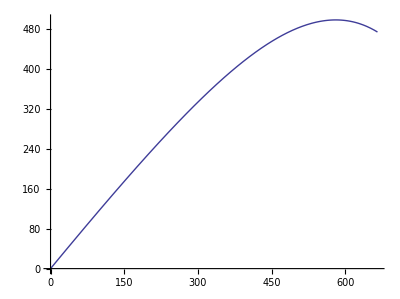

```mathematica
myplot1 = ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,10}];
Show[myplot1]
```

```mathematica
Manipulate[
g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```